```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

```mathematica
darkteal=RGBColor[1/256*{35,55,59}];
alertcolour=RGBColor[1/256*{235,129,27}];
```

```mathematica
checkers=Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
grid={EdgeForm[{Thin}],FaceForm[Transparent],#}&/@checkers;
blacks=Take[checkers,{1,-1,2}];
whites={White,#}&/@Drop[checkers,{1,-1,2}];
```

```mathematica
Graphics@{darkteal,grid,blacks}
```

-Graphics-

```mathematica
Export["Checkerboard.png",Graphics@{darkteal,grid,blacks},Background->None]
```

Checkerboard.png

```mathematica
Export["tealproto.png",Graphics[{darkteal,Rectangle[]}]]
Export["whiteproto.png",Graphics[{EdgeForm[{darkteal}],FaceForm[None],EdgeForm[Thick],Rectangle[]}],Background->None]
```

tealproto.png

whiteproto.png

```mathematica
Export["protoset.png",{Graphics[{darkteal,Rectangle[]}],Graphics[{EdgeForm[{darkteal}],FaceForm[None],Rectangle[]}]},Background->None]
```

protoset.png

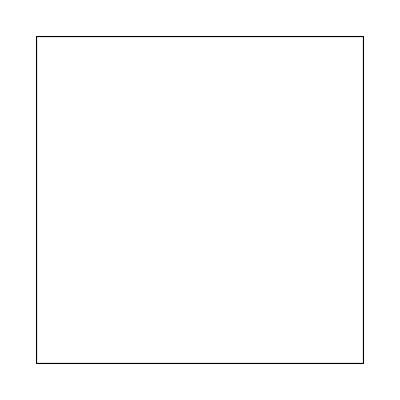
{-Graphics-,-Graphics-}

```mathematica
{Graphics[{darkteal,Rectangle[]}],Graphics[{EdgeForm[{darkteal}],FaceForm[None],EdgeForm[Thick],Rectangle[]}]}
```

```mathematica
newgrid=Complement[grid,Cases[grid,{EdgeForm[{Thickness[Tiny]}],FaceForm[-Graphics-],Translate[Rectangle[{0,0}],{4,_}]}]];
Translate[#,{0,0.5}]&/@Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]];
Complement[blacks,Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]]];
Graphics[{darkteal,newgrid,%%,%}]
Export["CheckerboardAperiodic.png",%, Background->None]
```

-Graphics-

CheckerboardAperiodic.png

```mathematica
Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
newblacks=Take[%,{1,-1,3}];
```

```mathematica
Graphics@{darkteal,grid,newblacks}
Export["CheckerboardOther.png",%,Background->None]
```

-Graphics-

CheckerboardOther.png

```mathematica
circles=Flatten[Table[Translate[Disk[],{i,j}],{i,0,7,2},{j,0,7,2}],1];
```

```mathematica
Rotate[Graphics[{FaceForm[darkteal],#}&/@circles],Pi/4];
Graphics[{darkteal,Rotate[circles,Pi/4]}];
Table[Graphics[{darkteal,Translate[Rotate[circles,Pi/4],{0,i*2Sqrt[2]}]}],{i,-2,1}];
Show[{%,%%},PlotRange->{{-2.3,8.3},{-3.75,6.85}}]
Export["CheckerboardCircles.png",%, Background->None, ImageResolution->200]
```

-Graphics-

CheckerboardCircles.png

-Graphics-

protodisk.png

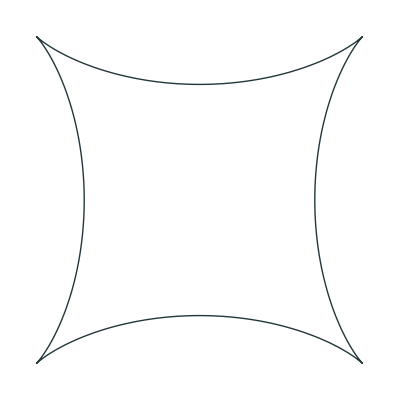

protosquare.png

```mathematica
Graphics[{darkteal,Disk[]}]
Export["protodisk.png",%, Background->None,ImageResolution->200]

a=Cos[t]^3;
b=Sin[t]^3;
ParametricPlot[{a Cos[Pi/4]-b Sin[Pi/4],a Sin[Pi/4]+b Cos[Pi/4]},{t,0,2Pi},Axes->None, PlotStyle->{darkteal,Thick}]
Export["protosquare.png",%, Background->None,ImageResolution->200]
```

```mathematica
Hexagon[x_]:=Line[x+#&/@(Through[{Cos,Sin}[Pi#/3]]&/@Range[0,6])]

HexagonalGrid[x_,y_]:=Module[{i,j},
Table[Hexagon[{3/2i,Sqrt[3]j+Mod[i,2]Sqrt[3]/2}],{i,x},{j,y}]
]
```

```mathematica
Graphics[{darkteal,Thick,#}&/@Flatten[HexagonalGrid[7,7],1],
PlotRange->{{.7,10.2},{.7,10.2}}]
Export["Hexagons.png",%,Background->None]
```

-Graphics-

Hexagons.png

```mathematica
Graphics[{Thick,darkteal,Hexagon[1]}]
Export["HexagonProto.png",%,Background->None]
```

-Graphics-

HexagonProto.png

```mathematica
Present:=Graphics[{Transpose[{((IfFat[#1,darkteal,alertcolour]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&
MakeCurveRulesPresent[{{A_,B_,C_},t_}]:=Module[{coors=Coor[{A,B,C}],littlelength=If[t=="fat",Abs[C-A],Abs[B-C]],biglength=If[t=="fat",Abs[B-A],Abs[C-A]],Aθ1=Arg[B-A],Aθ2=Arg[C-A],Bθ1=Arg[A-B],Bθ2=Arg[C-B]},littleradius=littlelength/(1+ϕ);bigradius=littlelength-littleradius;coorA=coors⟦1⟧;coorB=coors⟦2⟧;coorC=coors⟦3⟧;orientation=Sign[Det[Transpose[{coorA-coorB,coorC-coorB}]]];{Aθ1,Aθ2}=(If[orientation==1,CW[#1],CCW[#1]]&)[{Aθ1,Aθ2}];{Bθ1,Bθ2}=(If[orientation==1,CCW[#1],CW[#1]]&)[{Bθ1,Bθ2}];Color1=Lime;Color2=NiceBlue;If[t=="fat",{{Thick,Color1,Circle[coorA,bigradius,{Aθ1,Aθ2}]},{Thick,Color2,Circle[coorB,littleradius,{Bθ1,Bθ2}]}},{{Thick,Color1,Circle[coorA,littleradius,{Aθ1,Aθ2}]},{Thick,Color2,Circle[coorB,littleradius,{Bθ1,Bθ2}]}}]]
```

```mathematica
Present@FullInflate[{unitfat},0];
Export["FatProto.png",%,Background->None,ImageResolution->200]
Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@Inflate[{unitfat},0]];
Show[%%%,%]
Export["FatProtoRules.png",%,Background->None,ImageResolution->200]
Present@FullInflate[{unitskinny},0];
Export["SkinnyProto.png",%,Background->None,ImageResolution->200]
Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@Inflate[{unitskinny},0]];
Show[%%%,%]
Export["SkinnyProtoRules.png",%,Background->None,ImageResolution->200]
```

FatProto.png

-Graphics-

FatProtoRules.png

SkinnyProto.png

-Graphics-

SkinnyProtoRules.png

```mathematica
Present@FullInflate[{unitskinny},2];
Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@Inflate[{unitskinny},2]];
Show[%%,%]
```

-Graphics-

```mathematica
Present@FullInflate[{unitfat},1];
Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@Inflate[{unitfat},1]];
fat=Show[%%,%]
```

-Graphics-

```mathematica
FullInflate[{unitfat},1]
```

{{{-0.309017-0.363271 ⅈ,-0.5-0.951057 ⅈ,1.11022×10^-16-0.587785 ⅈ,0.190983},skinny},{{-0.309017+0.363271 ⅈ,-0.5+0.951057 ⅈ,1.11022×10^-16+0.587785 ⅈ,0.190983},skinny},{{0.190983,-0.309017+0.363271 ⅈ,-0.809017,-0.309017-0.363271 ⅈ},fat},{{0.809017,0.618034-0.587785 ⅈ,1.11022×10^-16-0.587785 ⅈ,0.190983},fat},{{0.809017,0.618034+0.587785 ⅈ,1.11022×10^-16+0.587785 ⅈ,0.190983},fat}}

```mathematica
locality={{{0.8090169943749475,0.6180339887498951-0.5877852522924732 ⅈ,1.1102230246251565*^-16-0.5877852522924732 ⅈ,0.19098300562505244},"fat"},{{0.8090169943749475,0.6180339887498951+0.5877852522924732 ⅈ,1.1102230246251565*^-16+0.5877852522924732 ⅈ,0.19098300562505244},"fat"}};
localityshifted={{{0.8090169943749475,0.6180339887498951-0.5877852522924732 ⅈ,1.1102230246251565*^-16-0.5877852522924732 ⅈ,0.19098300562505244}+2*0.5877852522924732 ⅈ,"fat"},{{0.8090169943749475,0.6180339887498951+0.5877852522924732 ⅈ,1.1102230246251565*^-16+0.5877852522924732 ⅈ,0.19098300562505244}+2*0.5877852522924732 ⅈ,"fat"}};
slide=-0.405+0.294I
skinny=Show[Present@{{{5.551115123125783*^-17+0.3632712640026805 ⅈ,0.1909830056250526+0.9510565162951538 ⅈ,-0.3090169943749474+0.5877852522924732 ⅈ,-0.5}*Exp[I (Pi/5+Pi)]+slide,"skinny"}},Graphics[MakeCurveRulesPresent/@AddRhombTris@{{{5.551115123125783*^-17+0.3632712640026805 ⅈ,-0.3090169943749474+0.5877852522924732 ⅈ,0.1909830056250526+0.9510565162951535 ⅈ}* Exp[I (Pi/5+Pi)]+slide,"skinny"}}]];

MakeCurveRulesPresent/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]};

Rotate[Show[Present@locality,Present@localityshifted,
Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]}],Graphics[Translate[MakeCurveRulesPresent/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]},{0,2*0.5877852522924732}]]],-Pi/2]
Export["Mistake.png",%,Background->None,ImageResolution->200]
Rotate[Show[Present@locality,Present@localityshifted,
Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]}],Graphics[Translate[MakeCurveRulesPresent/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]},{0,2*0.5877852522924732}]],skinny],-Pi/2]
Export["MistakeNext.png",%,Background->None,ImageResolution->200]
```

-0.405+0.294 ⅈ

-Graphics-

Mistake.png

-Graphics-

MistakeNext.png

```mathematica
Show[Present@Inflate[{unitfat},1],Graphics[MakeCurveRulesPresent/@Inflate[{unitfat},1]],Graphics[Text[Style["ϕ",Large],{-0.6,0.25}]],Graphics[Text[Style["1",Large],{-0.2,0.53}]],Graphics[Text[Style["ϕ",Large],{-0.35,-0.08}]],Graphics[Text[Style["1",Large],{0.5,-0.08}]]];
Export["RobFatSub.png",%,Background->None,ImageResolution->200];
Show[Present@Inflate[{unitskinny},1],Graphics[MakeCurveRulesPresent/@Inflate[{unitskinny},1]],Graphics[Text[Style["ϕ",Large],{-0.3,1}]],Graphics[Text[Style["1",Large],{-0.5,0.3}]]];
Export["RobSkinnySub.png",%,Background->None,ImageResolution->200];
Show[Present@FullInflate[{unitfat},1],Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@Inflate[{unitfat},1]]];
Export["RhombFatSub.png",%,Background->None,ImageResolution->200];
Show[Present@FullInflate[{unitskinny},1],Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@Inflate[{unitskinny},1]]];
Export["RhombSkinnySub.png",%,Background->None,ImageResolution->200];
```

```mathematica
Show[Present@{unitfat},Graphics[MakeCurveRulesPresent/@{unitfat}]];
Export["FatRob.png",%,Background->None, ImageResolution->200];
Show[Present@{unitskinny},Graphics[MakeCurveRulesPresent/@{unitskinny}]];
Export["SkinnyRob.png",%,Background->None, ImageResolution->200];
Show[Present@FullInflate[{unitfat},0],Graphics[MakeCurveRulesPresent/@AddConj@{unitfat}]];
Export["FatRhomb.png",%,Background->None, ImageResolution->200];
Show[Present@FullInflate[{unitskinny},0],Graphics[MakeCurveRulesPresent/@AddConj@{unitskinny}]];
Export["SkinnyRhomb.png",%,Background->None, ImageResolution->200];
```

```mathematica
SeeEdgesPresent:=Graphics[{EdgeForm[{White,Dashed}],FaceForm[None],Opacity[1],{Transpose[{((IfFat[#1,White,White]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}}]&

Show[Present@FullInflate[{unitfat},1],Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@Inflate[{unitfat},1]],SeeEdgesPresent@{unitfat}];
Export["RhombFatSubEdge.png",%,Background->None,ImageResolution->200];
Show[Present@FullInflate[{unitskinny},1],Graphics[MakeCurveRulesPresent/@AddConj@AddRhombTris@Inflate[{unitskinny},1]],SeeEdgesPresent@{unitskinny}];
Export["RhombSkinnySubEdge.png",%,Background->None,ImageResolution->200];
```

RhombSkinnySubEdge.png

```mathematica
Table[Export["Inflate"<>ToString[i]<>".png",Show[Present@FullInflate[{unitfat},i],Graphics[MakeCurveRulesPresent/@AddRhombTris@AddConj@Inflate[{unitfat},i]]],Background->None,ImageResolution->200],{i,0,5}];
```

{Inflate0.png,Inflate1.png,Inflate2.png,Inflate3.png,Inflate4.png,Inflate5.png}

```mathematica
Export["Inflate"<>ToString[10]<>".png",Show[Present@FullInflate[{unitfat},10]],Background->None,ImageResolution->200];
```

Inflate10.png

```mathematica
Export["Inflate11.png",Show[Present@FullInflate[{unitfat},11],PlotRange->{{-0.4,0.4},{-0.3,0.3}}],Background->None,ImageResolution->200];
```

Inflate11.png

```mathematica
inflate11=Present@FullInflate[{unitfat},11];
```

```mathematica
Show[inflate11, Graphics[List[Thickness[Large],StrokeForm[NiceGreen],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.04572085008615734,-0.000057438253877023504],0.037219988512349256]]],PlotRange->{{-0.4,0.4},{-0.3,0.3}}];
Export["PatternFind1.png",%,Background->None,ImageResolution->200];
```

PatternFind1.png

```mathematica
Show[inflate11,Graphics[List[Thickness[Large],StrokeForm[NiceRed],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.04572085008615734,-0.000057438253877023504],2*ϕ*0.037219988512349256+0.037219988512349256]]],Graphics[List[Thickness[Large],StrokeForm[NiceGreen],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.04572085008615734,-0.000057438253877023504],0.037219988512349256]]],PlotRange->{{-0.4,0.4},{-0.3,0.3}}];
Export["PatternFind2.png",%,Background->None,ImageResolution->200];
```

PatternFind2.png

```mathematica
Show[inflate11,
Graphics[List[Thickness[Large],StrokeForm[NiceRed],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.04572085008615734,-0.000057438253877023504],2*ϕ*0.037219988512349256+0.037219988512349256]]],Graphics[List[Thickness[Large],StrokeForm[NiceGreen],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.04572085008615734,-0.000057438253877023504],0.037219988512349256]]],
Graphics[List[Thickness[Large],StrokeForm[NiceBlue],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.0002154011847065318,0.13801830910070007],0.037219988512349256]]],
PlotRange->{{-0.4,0.4},{-0.3,0.3}}];
Export["PatternFind3.png",%,Background->None,ImageResolution->200];
```

PatternFind3.png

```mathematica
Show[inflate11,
Graphics[List[Thickness[Large],StrokeForm[NiceGreen],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[-0.04434233199310744,-0.0005169442848937111],0.05491145135923109]]],Graphics[List[Thickness[Large],StrokeForm[NiceRed],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[-0.04434233199310744,-0.0005169442848937111],2*ϕ*0.05491145135923109+0.05491145135923109]]],
PlotRange->{{-0.4,0.4},{-0.3,0.3}}];
Export["PatternFind4.png",%,Background->None,ImageResolution->200];
```

```mathematica
Show[inflate11,
Graphics[List[Thickness[Large],StrokeForm[NiceGreen],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[-0.04434233199310744,-0.0005169442848937111],0.05491145135923109]]],Graphics[List[Thickness[Large],StrokeForm[NiceRed],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[-0.04434233199310744,-0.0005169442848937111],2*ϕ*0.05491145135923109+0.05491145135923109]]],
Graphics[{Thickness[Large],StrokeForm[NiceBlue],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[{0.19226519337016573,-0.001043585021485549},0.05521423116447455]}],
PlotRange->{{-0.4,0.4},{-0.3,0.3}}];
Export["PatternFind5.png",%,Background->None,ImageResolution->200];
```

PatternFind5.png

```mathematica
tiling=FullInflate[starseed,2];
pathtris=Midpoints/@MakePathTriangles@tiling;
SeeTriPresent[points_]:=Graphics[{EdgeForm[White],FaceForm[None],Polygon[Coor[points]]}]
```

```mathematica
Show[Present@tiling];
Show[Present@tiling,SeeTriPresent/@pathtris];
Show[Present@tiling,SeeTriPresent/@pathtris,Graphics[{PointSize[Large],NiceRed,Point[Coor@{pathtris[[1,3]]}]}]];
Show[Present@tiling,SeeTriPresent/@pathtris,Graphics[{Lime,Thickness[Large],#}]&/@{GeneratePath[{pathtris,1,3,-1}][[1]]},Graphics[{PointSize[Large],NiceRed,Point[Coor@{pathtris[[1,3]]}]}]];
Show[Present@tiling,SeeTriPresent/@pathtris,Graphics[{Lime,Thickness[Large],#}]&/@{GeneratePath[{pathtris,1,3,-1}][[1;;2]]},Graphics[{PointSize[Large],NiceRed,Point[Coor@{pathtris[[1,3]]}]}]];
Show[Present@tiling,SeeTriPresent/@pathtris,Graphics[{Lime,Thickness[Large],#}]&/@{GeneratePath[{pathtris,1,3,-1}][[1;;3]]},Graphics[{PointSize[Large],NiceRed,Point[Coor@{pathtris[[1,3]]}]}]];
Show[Present@tiling,SeeTriPresent/@pathtris,Graphics[{Lime,Thickness[Large],#}]&/@{GeneratePath[{pathtris,1,3,-1}][[1;;4]]},Graphics[{PointSize[Large],NiceRed,Point[Coor@{pathtris[[1,3]]}]}]];
Show[Present@tiling,SeeTriPresent/@pathtris,Graphics[{Lime,Thickness[Large],#}]&/@{GeneratePath[{pathtris,1,3,-1}][[1;;All]]},Graphics[{PointSize[Large],NiceRed,Point[Coor@{pathtris[[1,3]]}]}]];
```

```mathematica
largetiling=FullInflate[starseed,7];
largepathtris=Midpoints/@MakePathTriangles@largetiling;
```

```mathematica
Show[Present@largetiling,Graphics[{Lime,Thickness[Large],#}]&/@GeneratePath[{largepathtris,80,1,1}],Graphics[{PointSize[Large],NiceRed,Point[Coor@{largepathtris[[80,1]]}]}]];
```

```mathematica
Table[Show[Present@largetiling,Graphics[{Lime,Thickness[Large],#}]&/@GeneratePath[{largepathtris,n,1,1}],Graphics[{PointSize[Large],NiceRed,Point[Coor@{largepathtris[[n,1]]}]}]],{n,100,800,50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[Present@largetiling,Graphics[{Lime,Thickness[Large],#}]&/@GeneratePath[{largepathtris,n,1,1}],Graphics[{PointSize[Large],NiceRed,Point[Coor@{largepathtris[[n,1]]}]}]],{n,100,8000,50}]
```

$Aborted

```mathematica
Parallelize[Table[Show[Present@largetiling,Graphics[{Lime,Thickness[Large],#}]&/@GeneratePath[{largepathtris,n,1,1}],Graphics[{PointSize[Large],NiceRed,Point[Coor@{largepathtris[[n,1]]}]}]],{n,100,800,100}]]
```

Show::gcomb: Could not combine the graphics objects in ….

{Show[-Graphics-,GeneratePath[-Graphics-],-Graphics-],Show[-Graphics-,GeneratePath[-Graphics-],-Graphics-],Show[-Graphics-,GeneratePath[-Graphics-],-Graphics-],Show[-Graphics-,GeneratePath[-Graphics-],-Graphics-],Show[-Graphics-,GeneratePath[-Graphics-],-Graphics-],Show[-Graphics-,GeneratePath[-Graphics-],-Graphics-],Show[-Graphics-,GeneratePath[-Graphics-],-Graphics-],Show[-Graphics-,GeneratePath[-Graphics-],-Graphics-]}